## Control effort for a first-order system (Section 14.5)

```mathematica
Clear["Global`*"];
```

```mathematica
Wg= Integrate[ⅇ^(2λ t),{t,0,τ}]
```

(-1+ⅇ^(2 λ τ))/(2 λ)

```mathematica
umin=ⅇ^(λ(τ-t))1/Wg(xτ-ⅇ^(λ τ)x0)
```

(2 ⅇ^(λ (-t+τ)) (-ⅇ^(λ τ) x0+xτ) λ)/(-1+ⅇ^(2 λ τ))

```mathematica
effort =(xτ-ⅇ^(λ τ)x0)^2 1/Wg//Simplify
```

(2 (-ⅇ^(λ τ) x0+xτ)^2 λ)/(-1+ⅇ^(2 λ τ))

```mathematica
eq={x'[t]-λ x[t] ==umin,x[0]==x0}
```

{-λ x[t]+x'[t]==(2 ⅇ^(λ (-t+τ)) (-ⅇ^(λ τ) x0+xτ) λ)/(-1+ⅇ^(2 λ τ)),x[0]==x0}

```mathematica
xs=DSolveValue[eq,x[t],t]//ExpToTrig//Simplify  (* invariant for λ -> -λ  *)
```

Csch[λ τ] (xτ Sinh[t λ]-x0 Sinh[λ (t-τ)])

```mathematica
xs/.t->{0,τ}//Simplify
```

{x0,xτ}

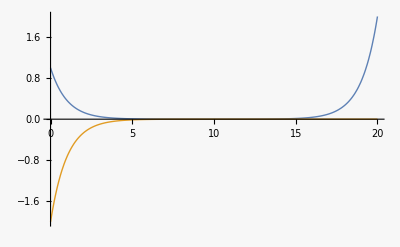

```mathematica
tmax=20;pars0={λ->1,x0->1,xτ->2,τ->tmax};
Plot[{xs/.pars0,umin/.pars0},{t,0,tmax},PlotRange->All]
```

```mathematica
umin/.{λ->1,x0->1,xτ->1}//FullSimplify
```

-2/(ⅇ^t+ⅇ^(t-τ))

Conclusion:  	Fast ops (τ <<  λ^-1):  effort ~(xτ - x0)^2/τ
			Slow ops (τ >>  λ^-1):  effort ratio ~ ⅇ^(2|λ|τ)
			The zero in effort is for the natural (uncontrolled, with u=0) protocol.  If you ask for the right 				xtau and the right tau, this works.

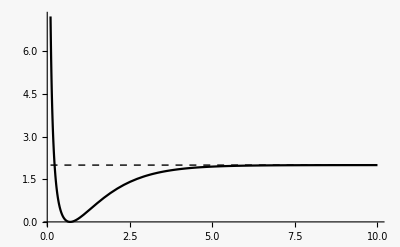

```mathematica
pars={λ->1,x0->1,xτ->2};
Plot[{effort/.pars,2λ x0^2/.pars},{τ,0.1,10},PlotRange->All,PlotStyle->{Black,{Black,Thin,Dashed}}]
```